50

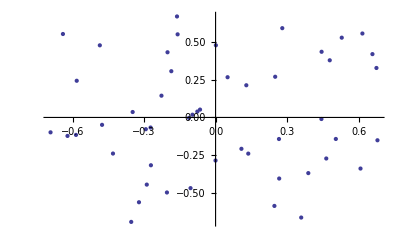

```mathematica
(*Plot a random set of points in the unit square*)
npts=50
ls=RandomReal[{-.7,.7},{npts,2}];
ListPlot[ls]
```

```mathematica
(*Create a map function that takes distances and produces a relatedness score. HEre relatedness inverseley proportional to distance cubed (only reason--it made nicer figures*)
f=RandomVariate[ PoissonDistribution[1/10000/(#^3+0.000000000001)]]& (*# is the distance between two points*)
```

RandomVariate[PoissonDistribution[1/(10000 (#1^3+1.×10^-12))]]&

```mathematica
(*Find element-by-element minimum of two arbitrary matrices*)
matrixmin[mat1_,mat2_]:=(mat1+mat2)/2-Abs[mat1-mat2]/2
(*traintrack distance. We first rotate the points by angle theta, then project to horizontal line with y-intercept at pos *)
d1[ls_,pos_,θ_]:=Module[{strip,lsrot},lsrot=Dot[ls,RotationMatrix[θ]];strip=Map[Abs,lsrot⟦1;;,2⟧-pos];Outer[Plus,strip,strip]]

(*Simulate a dataset assuming a traintrack at specified position*)
simulatepos=.3
simulateθ=Pi/4
(*define Euclidean distance matrix for set of points*)
d0=Table[Norm[ls⟦i⟧-ls⟦j⟧],{i,1,npts},{j,1,npts}];
tab=matrixmin[d0,d1[ls,simulatepos,simulateθ]]; (*Distances are the minimum of Euclidean and traintrack.*)
edges=Map[f,tab,{2}]; (*Generate the simulated IBD segments*)
For [i=1,i≤npts,i+=1,edges⟦i,i⟧=0] (*Set diagonal terms to zero.*)
```

0.3

π/4

```mathematica
(*tab=Table[d[ls⟦i⟧,ls⟦j⟧],{i,1,npts},{j,1,npts}];*)
```

```mathematica
(*Plot all IBD segments--only those with nonzero IBD*)
fplot[i_,j_]:=If[edges⟦i,j⟧>0 && i≠j,Sow[ListPlot[{ls⟦i⟧,ls⟦j⟧},Joined->True,PlotStyle->Thickness[tab⟦i,j⟧*0.01]]]]
```

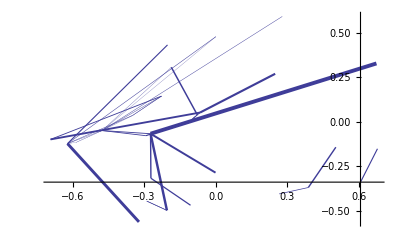

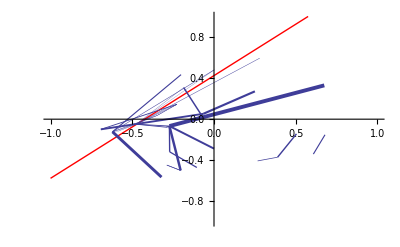

```mathematica
tplot=Reap[Table[fplot[i,j],{i,1,npts},{j,1,npts}]];
plot0=Show[tplot⟦2,1⟧,PlotRange->All]
Show[Plot[{x Tan[θ]-a/.{θ->simulateθ,a->-simulatepos/Cos[simulateθ]}},{x,-1,1},PlotStyle->Red,PlotRange->{-1,1}],plot0]
```

```mathematica
(*Measure the correlation given a, θ, and the list of points ls. edges is defined globally*)
correl[ls_,a_,θ_]:=Correlation[Flatten[matrixmin[d0,d1[ls,a,θ]]],Flatten[edges] ]^2
```

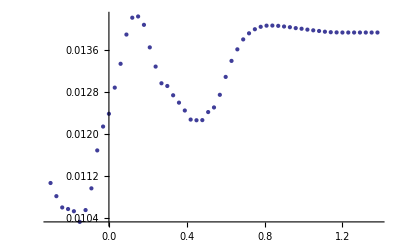

```mathematica
(*Calculate the correlation vs position. The squared correlation should be maximized at 0.8 *)
ListPlot[Table[{a,correl[ls,a,0]},{a,-.3,1.4,.03}],PlotRange->All]
```

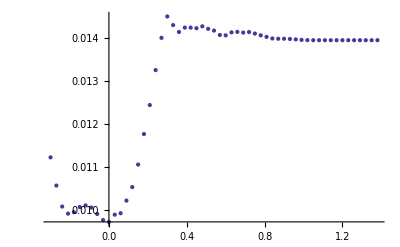

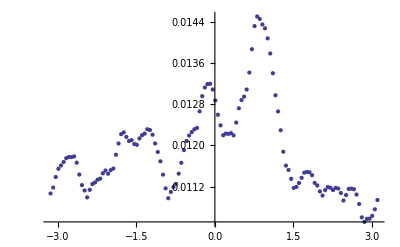

```mathematica
ListPlot[Table[{a,correl[ls,a,simulateθ]},{a,-.3,1.4,.03}],PlotRange->All]
ListPlot[Table[{θ,correl[ls,simulatepos,θ]},{θ,-Pi,Pi,.05}],PlotRange->All]
```

```mathematica
(*Maximize likelihood. It is a hard simulation problem, so start near the minimum to test convergence*)
pmax=FindMinimum[correl[ls,a,θ],{{θ,simulateθ},{a,simulatepos}},AccuracyGoal->2,PrecisionGoal->2]
```

```mathematica
(*Or just do a grid search*)
foo=ParallelTable[correl[ls,a,θ],{θ,0,Pi,0.1},{a,-1,1,0.1}];
mmax=Max[Map[Max,foo]]
pmax=Position[foo,mmax]
vals=Table[{a,θ},{θ,0,Pi,0.1},{a,-1,1,0.1}];
{amax,tmax}=vals⟦pmax⟦1,1⟧,pmax⟦1,2⟧⟧
```

$Aborted

0.0145

{{9,14}}

{0.3,0.8}

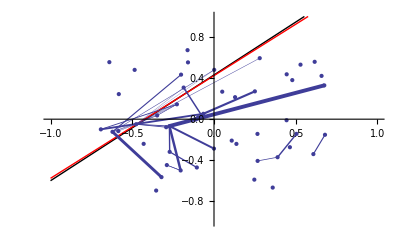

```mathematica
Show[Plot[{x Tan[tmax]-aa/.aa->-amax/Cos[tmax],x Tan[θ]-a/.{θ->simulateθ,a->-simulatepos/Cos[simulateθ]}},{x,-1,1},PlotStyle->{{Thick,Black},{Thick,Red}},PlotRange->{-1,1}],plot0,ListPlot[ls]]
```

```mathematica
(*Try to maximize likelihood with experimental optimizer--feel free to ignore.*)
dim=2
verbose=2
down[-correl[ls,#⟦1⟧,#⟦2⟧]&,100,0.0000001]
```

2

2

starting positions {-0.405534,-0.0943548} {0.217072,0.0174376}

val 1 {-0.02135758,{xx[1]→-0.4107332,xx[2]→-0.09449513}}

Initialized target to -0.0192218

Entering loop -0.0192218

iteration1

Got delta -0.0192218

updated target to -0.0213576

Tested delta-0.0213576

got near{{-0.4107332,-0.09449513},{-0.405534,-0.0943548}}

got nnear{-0.405534,-0.0943548}

got fnear-0.0213084

got step-0.0213576

found fixed point{-0.4107332,-0.09449513} {-0.405534,-0.0943548}

{-0.0213576,{-0.4107332,-0.09449513}}